```mathematica
SetDirectory[NotebookDirectory[]];
```

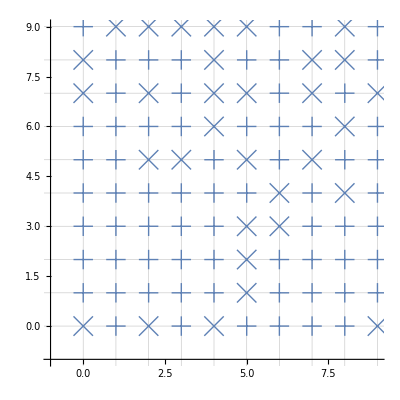

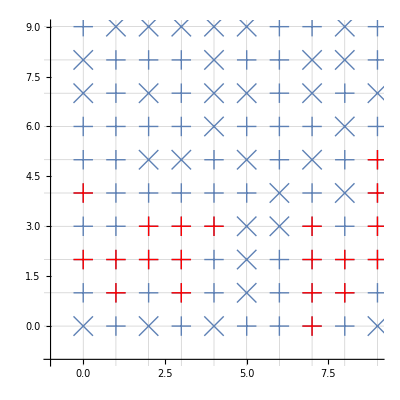

```mathematica
nodelist = Import["nodes.csv"];
clusterlist = Import["cluster.csv"];

grid={0,1,2,3,4,5,6,7,8,9,10};

points=Table[If[nodelist[[i]][[3]]==1,{nodelist[[i]][[1]],nodelist[[i]][[2]]},##&[]],{i,1,Length[nodelist]}];
spinupa=ListPlot[points,AxesOrigin->{-1,-1},AspectRatio->1,PlotMarkers->{"↑",20},GridLines->{grid,grid}];
spinupp=ListPlot[points,AxesOrigin->{-1,-1},AspectRatio->1,PlotMarkers->{"+",20},GridLines->{grid,grid}];

points=Table[If[nodelist[[i]][[3]]==-1,{nodelist[[i]][[1]],nodelist[[i]][[2]]},##&[]],{i,1,Length[nodelist]}];
spindowna=ListPlot[points,AxesOrigin->{-1,-1},AspectRatio->1,PlotMarkers->{"↓",20},GridLines->{grid,grid}];
spindownn=ListPlot[points,AxesOrigin->{-1,-1},AspectRatio->1,PlotMarkers->{"×",20},GridLines->{grid,grid}];

points=Table[If[clusterlist[[i]][[3]]==-1,{clusterlist[[i]][[1]],clusterlist[[i]][[2]]},##&[]],{i,1,Length[clusterlist]}];
clusterupa=ListPlot[points,AxesOrigin->{-1,-1},AspectRatio->1,PlotMarkers->{"↑",20},PlotStyle->{Red}];
clusterupp=ListPlot[points,AxesOrigin->{-1,-1},AspectRatio->1,PlotMarkers->{"+",20},PlotStyle->{Red}];
points=Table[If[clusterlist[[i]][[3]]==1,{clusterlist[[i]][[1]],clusterlist[[i]][[2]]},##&[]],{i,1,Length[clusterlist]}];
clusterdowna=ListPlot[points,AxesOrigin->{-1,-1},AspectRatio->1,PlotMarkers->{"↓",20},PlotStyle->{Red}];
clusterdownn=ListPlot[points,AxesOrigin->{-1,-1},AspectRatio->1,PlotMarkers->{"×",20},PlotStyle->{Red}];

Show[spinupa,spindowna];
Show[spinupp,spindownn]
Show[clusterupa];
Show[clusterdowna];
Show[clusterupp];
Show[clusterdownn];
Show[spinupa,spindowna,clusterupa,clusterdowna];
Show[spinupp,spindownn,clusterupp,clusterdownn]
```

```mathematica
2*128^2*0.0175
```

573.44

{1,0}

{10001,-40.3025}

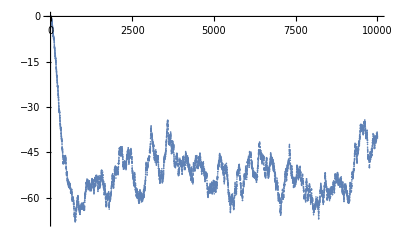

{1,0}

{10001,-0.00128174}

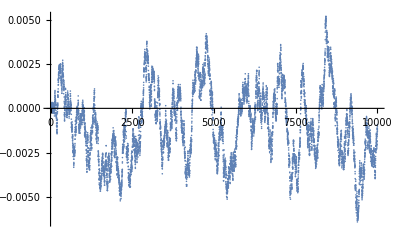

{1,0.01}

{128,0.001226}

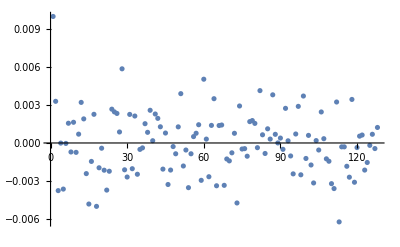

```mathematica
energies = Import["energy.dat","Table"];
energies=Table[{i,energies[[i]][[1]]},{i,1,Length[energies]}];
energies[[1]]
energies[[Length[energies]]]
ListPlot[energies,PlotRange->All]
mag = Import["magnetization.dat","Table"];
mag=Table[{i,mag[[i]][[1]]},{i,1,Length[mag]}];
mag[[1]]
mag[[Length[mag]]]
ListPlot[mag,PlotRange->All]
corr = Import["correlation.dat","Table"];
corr=Table[{i,corr[[i]][[1]]},{i,1,Length[corr]}];
corr[[1]]
corr[[Length[corr]]]
ListPlot[corr,PlotRange->All]
```

{1,1.}

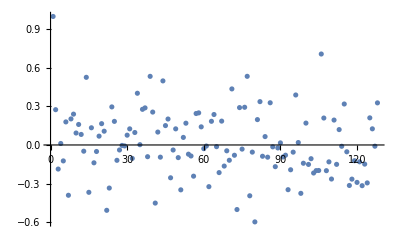

{1,1.}

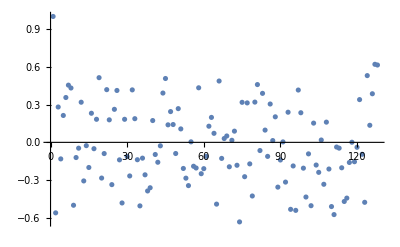

{1,1.}

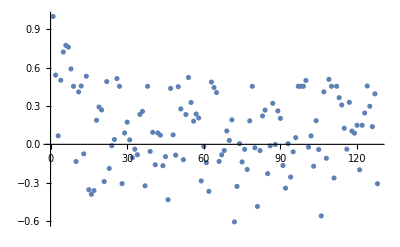

```mathematica
energies = Import["~/phd-stuff/courses/comp_phys/mp256256_T300_J00175_bmin_s1m/correlation.dat","Table"];
energies=Table[{i,100energies[[i]][[1]]},{i,1,Length[energies]}];
energies[[1]]
ListPlot[energies,PlotRange->All]
energies = Import["~/phd-stuff/courses/comp_phys/mp256256_T300_J00175_b05_s1m/correlation.dat","Table"];
energies=Table[{i,100energies[[i]][[1]]},{i,1,Length[energies]}];
energies[[1]]
ListPlot[energies,PlotRange->All]
energies = Import["~/phd-stuff/courses/comp_phys/mp256256_T300_J00175_bmax_s500k/correlation.dat","Table"];
energies=Table[{i,100energies[[i]][[1]]},{i,1,Length[energies]}];
energies[[1]]
ListPlot[energies,PlotRange->All]
```

{1,-1.1}

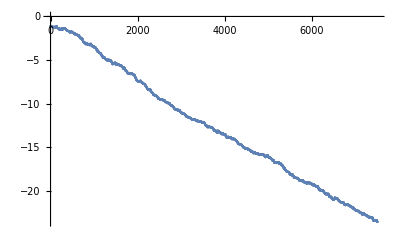

{1,13.16}

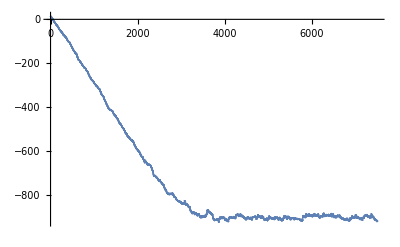

{1,1.56}

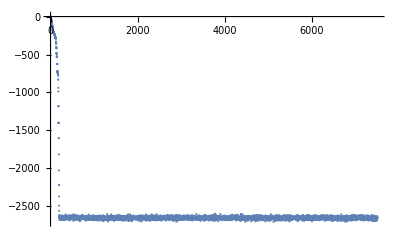

```mathematica
energies = Import["~/phd-stuff/courses/comp_phys/p256256_T300_J0005_b05_s7d5k/energy.dat","Table"];
energies=Table[{i,energies[[i]][[1]]},{i,1,Length[energies]}];
energies[[1]]
ListPlot[energies,PlotRange->All]
energies = Import["~/phd-stuff/courses/comp_phys/p256256_T300_J00175_b05_s7d5k/energy.dat","Table"];
energies=Table[{i,energies[[i]][[1]]},{i,1,Length[energies]}];
energies[[1]]
ListPlot[energies,PlotRange->All]
energies = Import["~/phd-stuff/courses/comp_phys/p256256_T300_J003_b05_s7d5k/energy.dat","Table"];
energies=Table[{i,energies[[i]][[1]]},{i,1,Length[energies]}];
energies[[1]]
ListPlot[energies,PlotRange->All]
```

```mathematica
N[2/(Log[1+Sqrt[2]])]*0.0175/(8.6173303*10^-5)
```

460.824

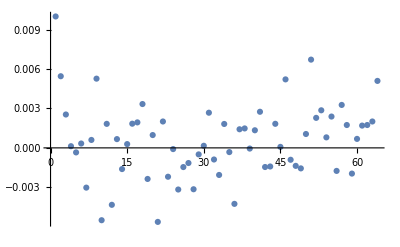

```mathematica
correlation = Import["correlation.dat","Table"];
correlation=Table[{i,correlation[[i]][[1]]},{i,1,Length[correlation]}];
ListPlot[correlation,PlotRange->All]
```

```mathematica
"512px T = 300 J = 0.0175 Bias = 1.0 steps = 10k"
```

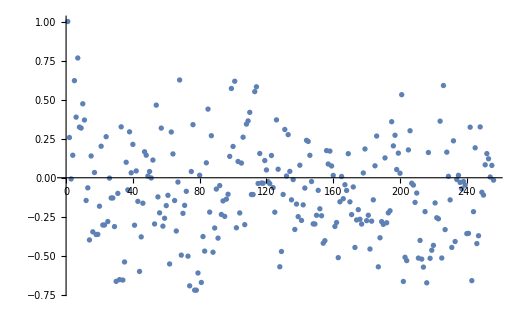

```mathematica
"512px T = 300 J = 0.015 Bias = 1.0 steps = 10k"
```

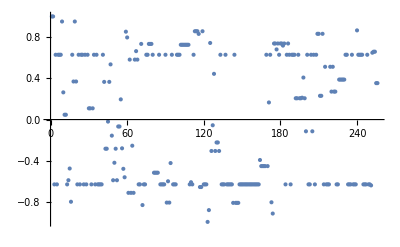

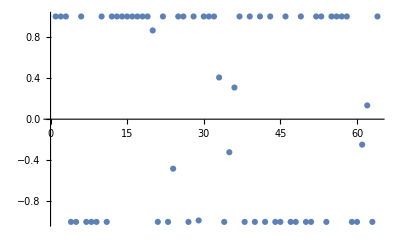

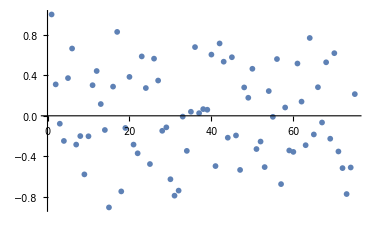

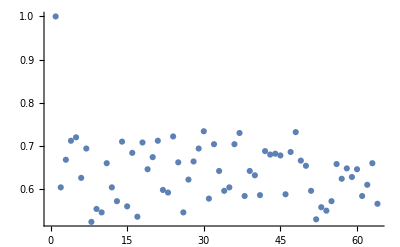

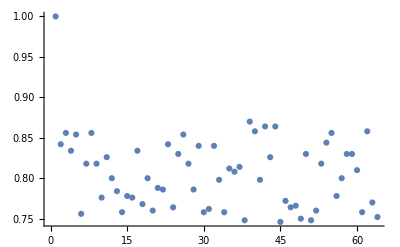

```mathematica
correlation = Import["correlation.dat","Table"];
Mean[correlation]
```

{-0.0812281}